# Randomized Benchmarking For Stabilizer Codes

## Settings and Common Operators

### Settings

```mathematica
$PrePrint=Switch[#,
_?ArrayQ,Switch[#,
		_?(Function[mat,Dimensions[mat]== {5,2,2}]),MatrixForm[Chop[Sequence@@@#,Prec]],
		_?(Function[mat,Times@@Dimensions[mat]≤ 32^2]),MatrixForm[Chop[#,Prec]],
		_,#],
_,#]&;

MyPrint=Print@$PrePrint[#]&;

SetOptions[EvaluationNotebook[],CodeAssistOptions->{"FloatingElementEnable"->False}]
```

```mathematica
Needs["HypothesisTesting`"]
Needs["Developer`"]
```

### Operators and Constants

```mathematica
Code = {5,1,3};
Prec = .000001;
SA=SparseArray;
MatPow=MatrixPower;
Zero =SA[({{0., 0.}, {0., 0.}})];
Id [d_] :=SA[{i_,j_}/;i== j:>1.,{d,d}];
X =SA[({{0, 1.}, {1., 0}})];
Y=SA[I({{0, -1.}, {1., 0}})];
Z= SA[({{1., 0}, {0, -1.}})];
H=SA[1/(√2)({{1., 1.}, {1., -1.}})];
P=SA[({{1., 0}, {0, I}})];
HP=H.P; 
CommonSingleQubitGates={Id[2],X,Y,Z,H,P,HP};
CNOT=SA[({{1., 0., 0, 0}, {0., 1., 0, 0.}, {0, 0, 0, 1.}, {0, 0, 1., 0}})];
SWAP=SA[({{1., 0., 0, 0}, {0., 0., 1., 0}, {0, 1., 0, 0}, {0, 0, 0, 1.}})];
NS=CNOT.SWAP;
SN=SWAP.CNOT;

(*Perfect Gates with no rounding for applications requiring many multiplications*)
PId [d_] :=SA[{i_,j_}/;i== j:>1,{d,d}];
PX =SA[({{0, 1}, {1, 0}})];
PY=SA[I({{0, -1}, {1, 0}})];
PZ= SA[({{1, 0}, {0, -1}})];
(* THERE IS NO PHASE HADAMARD!! PH mea *)
PH=SA[1/(√2)({{1, 1}, {1, -1}})];
PP=SA[({{1, 0}, {0, I}})];
PHP=PH.PP;
PCNOT=SA[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}})];
PSWAP=SA[({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})];
SingleQubitPaulis={Id[2],X,Y,Z};
SingleQubitPauliStrings={"I","X","Y","Z"};
SingleQubitPaulisToStringForm=AssociationThread[SingleQubitPaulis-> SingleQubitPauliStrings];

(* Zero if they commute, 1 if they don't *)
Commutes[gate1_?MatrixQ,gate2_?MatrixQ]:=Commutes[gate1,gate2]=If[gate1.gate2== gate2.gate1,0,1];

(* memoize at single qubit level *)
SingleQubitMult[gate1_,gate2_]:=SingleQubitMult[gate1,gate2]=Dot[gate1,gate2];
SingeQubitCT[gate_] := SingleQubitCT[gate] = CT[gate];
```

```mathematica
SingleQubitHGroup = {PId[2], PX, PY, PZ, PH, PH.PX, PH.PY, PH.PZ};
SingleQubitPGroup = {PId[2], PX, PY, PZ, PP, PP.PX, PP.PY, PP.PZ};
SingleQubitAsymGroup = {Id[2],X,Y,Z,P.H,H.P,P.H.X,P.H.Y,P.H.Z,H.P.X,H.P.Y,H.P.Z};
SingleQubitCGroup=Join[SingleQubitPGroup,H.#&/@SingleQubitPGroup,#.H&/@SingleQubitPGroup];
```

### General Purpose Functions

```mathematica
(*Enact gate g on ith qubit*)
Gate[g_?MatrixQ, i_?IntegerQ]:= (Gate[g,i]=KroneckerProduct@@ListGate[g,i]);

MatNormalize[mat_]:=Chop[mat/√(First@( mat.CT[mat])["NonzeroValues"]),10*Prec]

CliffordQ[Liou_?MatrixQ]:= AllTrue[Total[Liou/._?(Abs[#]≥Prec&):>1,{1}],#== 1&]

GetPhaseofFirstNonZeroElement[mat_?MatrixQ]:=Sign[First@SA[mat]["NonzeroValues"]];
NormPhase[m_]:=NormPhase[m]=m/GetPhaseofFirstNonZeroElement[m];
KillSmallPhase[mat_?MatrixQ]:=GetPhaseofFirstNonZeroElement[mat]

WithinTol[m1_,m2_]:=If[Dimensions[m1]== Dimensions[m2],Norm[NormPhase[m1]- NormPhase[m2]]<Prec,False]

CGate::OperatorOverflow ="Only `1` Qubits provided for `2` Qubit Operation";
CGate[ins_?ListQ, outs_?ListQ,G_]:=(
If[Log[2,Length[G]]+Max[outs]-1>Code[[1]],Return[Message[CGate::OperatorOverflow ,Code[[1]],Log[2,Length[G]]+Max[outs]-1]];,];
Module[{sum=SA[{i_}/;i:>0,{2^Code[[1]],2^Code[[1]]}],num,Gcount=0},
For[d=0,d≤ 2^Length[ins]-1,d++,
num=IntegerDigits[d,2,Length[ins]];
sum=sum+KroneckerProduct@@Table[
If[Gcount≠  0,Gcount=Gcount-1;{1},
If[MemberQ[outs,j],
If[d== 2^Length[ins]-1,Gcount=Log[2,Length[G]]-1;G,Id[2]],
If[MemberQ[ins,j],
<|{0}->SA[({{1., 0}, {0, 0}})],{1}->SA[({{0, 0}, {0, 1.}})]|>[num[[FirstPosition[ins,j]]]]
,Id[2]]
]],{j,Code[[1]]}]];
sum])

getvarname[var_]:=SymbolName[Unevaluated@var]
SetAttributes[getvarname,HoldFirst]
```

Some general functions for evaluating quantum maps

```mathematica
ChoiBasisMatrix[i_,j_,n_]:=ChoiBasisMatrix[i,j,n]=KroneckerProduct[UnitVector[n,i],UnitVector[n,j]];
GetChoiMatrix[chan_,numq_]:=Sum[KroneckerProduct[ChoiBasisMatrix[i,j,2^numq],chan[ChoiBasisMatrix[i,j,2^numq]]],{i,Range[2^numq]},{j,Range[2^numq]}]
testchan[num_]:=testchan[num]=Table[Subscript[e, c1,c2],{c1,num},{c2,num}];

TPQ[chan_,numq_:Code[[1]]]:=If[TrueQ[Chop@Simplify@Abs[Tr[chan@testchan[2^numq]]-Tr[testchan[2^numq]]]<Prec],True, False]
CPQ[chan_,numq_:Code[[1]]]:=AllTrue[Chop[Eigenvalues@GetChoiMatrix[chan,numq],Prec],NonNegative]

CPTPQ[chan_,numq_:Code[[1]]]:=(TPQ[chan,numq]&&CPQ[chan,numq]);
```

### Function Shorthands

```mathematica
SA=SparseArray;
CT=ConjugateTranspose;
KP=KroneckerProduct;
MatPow=MatrixPower;
LMatPow:=ListPower;
LDot:=ListDot;
```

## Data Structures

We define basic properties of each and functions to convert between them. Note that some of these data structures are not general. So conversion is not always possible.

### "Full" Form

Full matrix in the usual representation of quantum mechanics

```mathematica
(*Works best with pauli gates. TODO: Extend to all decomposable gates*)
FullToList[mat_?MatrixQ]:= ListSetPhase[Flatten[Delete[NestList[ToListKPHelperFunc,{,mat},Log[2,Length[mat]]-1][[2;;]],Table[{i,2},{i,Log[2,Length[mat]]-2}]],1],GetPhaseofFirstNonZeroElement[mat]]
FullToSeparatePhase[mat_?MatrixQ]:=ListToSeparatePhase[FullToList[mat]]

ToListKPHelperFunc[m_]:= MatNormalize/@SA/@nearestKroneckerProduct[m[[2]],{2,2},{Length[m[[2]]]/2,Length[m[[2]]]/2}]
```

### “List” Form

list of 2 qubit gates represented as sparse arrays. Generally used to express Paulis and a limited set of Clifford gates.

```mathematica
ListToFull[gate_?ListQ]:=ListToFull[gate]= KroneckerProduct@@gate;
ListToSeparatePhase[gate_?ListQ]:={ListGetPhase[Chop[gate,Prec]],ListNormPhase[Chop[gate,Prec]]}

(* functions for dealing with lists of single qubit gates *)
ListDot[elems__]:=FoldList[SingleQubitMult@@@Partition[Riffle[#1,#2],2]&,{elems}][[Length[{elems}]]];
ListPower[m_,n_]:=If[n>0,Fold[ListDot,Table[m,{n}]],ListId]
ListCT[gate_?ListQ]:=SingeQubitCT/@gate;
ListId=LId=Table[Id[2],{Code[[1]]}];
ListZero=LZero=Table[Zero,{Code[[1]]}];

ListEqual[elems__]:=AllTrue[MapThread[QubitEqual,{elems}],#&]
LEqual=ListEqual;
Map2=Table[#2[[i]]~#~#2[[i+1]],{i,Length@#2-1}]&;
QubitEqual[elems__]:=AllTrue[Map2[Chop[NormPhase[#1]-NormPhase[#2],Prec]== Zero&,{elems}],#&]

ListToString[list_?ListQ]:=SingleQubitPaulisToStringForm /@list;

ListGetPhase[gate_?ListQ]:=Times@@GetPhaseofFirstNonZeroElement/@gate;
ListNormPhase[gate_?ListQ]:=NormPhase/@gate;
ListSetPhase[gate_?ListQ,phase_?NumberQ]:=ReplacePart[ListNormPhase[gate],1->ListNormPhase[ gate][[1]]*phase];

ListGate[g_?MatrixQ, i_?IntegerQ]:=ListGate[g,i]= Table[If[j== i,g,Id[2]],{j,Code[[1]]}];
ListCommutes[gate1_?ListQ,gate2_?ListQ]:=Mod[Total[Commutes@@@Partition[Riffle[gate1,gate2],{2}]],2];

ListHSInnerProd[gate1_,gate2_]:=ListHSInnerProd[gate1,gate2]=1/2^Code[[1]] Times@@Tr/@ListDot[ListCT@gate1,gate2];
```

#### “SeparatePhase” Form

A list containing an overall phase and a List object which has been reduced using SeparatePhaseToList. Used for debugging and displaying matrices.

```mathematica
SeparatePhaseDot[gates__]:=(DottedGates=ListDot@@{gates}[[;;, 2]];{Times@@{gates}[[;;,1]]*ListGetPhase[DottedGates],ListNormPhase[DottedGates]})
SeparatePhaseToFull[gate_?ListQ]:=ListToFull[SeparatePhaseToList[gate]];
SeparatePhaseToList[gate_?ListQ]:=ReplacePart[gate[[2]],1-> gate[[1]]*gate[[2,1]]];

SeparatePhaseCT[gate_?ListQ]:=(InnerCT=ListCT[gate[[2]]];{Conjugate[gate[[1]]]*ListGetPhase[InnerCT],ListNormPhase[InnerCT]});
SeparatePhaseSetPhase[gate_?ListQ,phase_?NumberQ]:=ReplacePart[gate,1-> gate[[1]]*phase];

SeparatePhaseToStringForm[gate_?ListQ]:=SeparatePhaseToStringForm[Chop[gate,10*Prec]]={Chop[PhaseFixer[gate[[2]]]*gate[[1]],Prec],NormPhaseSingleQubitPaulisToStringForm/@gate[[2]]};
PhaseFixer[normgate_?ListQ]:=(-I)^Count[Norm[#-NormPhase[Y]]<Prec&/@normgate,True]

StringToSeparatePhase[gate_?ListQ]:={gate[[1]],Sequence@@@PositionIndex[SingleQubitPaulisToStringForm]/@gate[[2]]}

NormPhaseSingleQubitPaulis=NormPhase/@SingleQubitPaulis;
NormPhaseSingleQubitPaulisToStringFormAssoc=AssociationThread[NormPhase/@SingleQubitPaulis-> SingleQubitPauliStrings];
NormPhaseSingleQubitPaulisToStringForm[pauli_]:=NormPhaseSingleQubitPaulisToStringFormAssoc[FirstCase[NormPhaseSingleQubitPaulis,_?(Norm[#- pauli]<Prec&),{1}]];
```

## Define A Stabilizer Code with Generators

```mathematica
Code = {5,1,3}; (*easy acess to properties of this code *)
SGens=
{{X,Z,Z,X,Id[2]},
{Z,Z,X,Id[2],X},
{Z,X,Id[2],X,Z},
{X,Id[2],X,Z,Z}};
DGens=
{{Y,Id[2],Id[2],Id[2],Y},
{Y,Id[2],Id[2],Y,Id[2]},
{Y,Id[2],Y,Id[2],Id[2]},
{Y,Y,Id[2],Id[2],Id[2]}};
LGens=
{{X,X,X,X,X},
{Z,Z,Z,Z,Z}};
PLGens=
{{PX,PX,PX,PX,PX},
{PZ,PZ,PZ,PZ,PZ}};
LHP={HP, HP,HP,HP,HP};
PLHP={PHP, PHP,PHP,PHP,PHP};
FullLHP=KroneckerProduct@@LHP;
AsymGens={Sequence@@PLGens,LHP};
FullAsymGens=KP@@@AsymGens;
PLGens={{PX,PX,PX,PX,PX},
{PZ,PId[2],PX,PX,PId[2]}};
FullLGens =KroneckerProduct@@@LGens;
FullSGens =KroneckerProduct@@@SGens;
FullDGens =KroneckerProduct@@@DGens;
LX={X,X,X,X,X};
LZ={Z,Z,Z,Z,Z};
LY={Y,Y,Y,Y,Y};
```

The Stabilizers, Pure errors, and Logicals can always be arranged into a sets of orthogonal conjugate variables. I assume that the Logicals are input with conjugate Paulis placed next to one another. We call this CodeConjugatePaulis because these are the variables which are defined on the code. Another simple example of Conjugate Paulis are X_i and Z_i for the ith qubit, I call this the “minimum weight” conjugate Paulis.

```mathematica
CodeConjugatePaulis={Sequence@@@{SGens, LGens[[;;;;2]]},Sequence@@@{DGens, LGens[[2;;;;2]]}};
MWConjugatePaulis={Table[ListGate[X,i],{i,Code[[1]]}],Table[ListGate[Z,i],{i,Code[[1]]}]};
```

Encoder for the 5 qubit code

```mathematica
Encoder= .KP[X.H,H,H,X.H,Id[2]]
```

## Define Groups Related to Code

```mathematica
AbelianGroupConstructor[InputGens_?ListQ, mult_:ListDot, pow_:ListPower]:= Module[{GenOrders,Gens},
Gens=Reverse[InputGens];
GenOrders=FindOrder/@Gens;

(* tells us how to make each element and where to put it in the final list *)
signatures=Tuples[Table[Range[0,Order-1],{Order,GenOrders}]];

Table[mult[Sequence@@MapThread[pow,{Gens,sig}]],{sig,signatures}]
];

FindOrder[elem_,mult_:ListDot]:=Length[NestWhileList[mult[#,elem]&,mult[elem,elem],Max[Abs[#- elem]]>Prec&]]
```

```mathematica
(* Constructs non-abelian groups as blocks. Find all products, eliminate duplicates, test for equality, repeat until no new elements added. VERY SLOW AND BAD *)
NonAbelianGroupConstructor::GroupSizeErr="Encountered size limit while enumerating Group elements. Group Size: '1'";
NonAbelianGroupConstructor[InputGens_,mult_:ListDot,equals_:ListEqual,Ident_:ListId, sizelimit_: 1000]:=Module[{Gens,NewGens,group={}},

If[InputGens[[1]]≠Ident,Gens=DeleteDuplicates[Prepend[InputGens,Ident]],Gens=DeleteDuplicates[InputGens]];

NewGens=DeleteDuplicates[Flatten[Outer[mult,Gens,Gens,1],1],equals];

While[Length[NewGens]!= Length[Gens]&& Length[Gens]< sizelimit,Gens=NewGens;NewGens=DeleteDuplicates[Flatten[Outer[mult,Gens,Gens,1],1],equals]];

If[Length[Gens]>sizelimit,Message[NonAbelianGroupConstructor::GroupSizeErr,Length[Gens]],];

Gens
]
```

```mathematica
SGroup=AbelianGroupConstructor[SGens];
DGroup=ListDDecoding=AbelianGroupConstructor[DGens];

Decoding=MWDecoding={Id[2^Code[[1]]],Gate[X,3],Gate[Z,5],Gate[X,2],Gate[Z,2],Gate[Z,4],Gate[X,1],Gate[Y,2],Gate[X,4],Gate[Z,1],Gate[Z,3],Gate[Y,3],Gate[X,5],Gate[Y,4],Gate[Y,5],Gate[Y,1]};
ListDecoding=ListMWDecoding={ListId,ListGate[X,3],ListGate[Z,5],ListGate[X,2],ListGate[Z,2],ListGate[Z,4],ListGate[X,1],ListGate[Y,2],ListGate[X,4],ListGate[Z,1],ListGate[Z,3],ListGate[Y,3],ListGate[X,5],ListGate[Y,4],ListGate[Y,5],ListGate[Y,1]};

(* Logical Parts for the minimum weight decoding *)
ListLogicalMWDecoding={ListId,LX,LZ,LX,LZ,LZ,LX,LY,LX,LZ,LZ,LY,LX,LY,LY,LY};
LogicalMWDecoding=KP@@@ListLogicalMWDecoding;

ListIdDecoding=Table[ListId,{2^(Code[[1]]-Code[[2]])}];
IdDecoding=KP@@@ListIdDecoding;

Decoding=MWDecoding=KP@@@ListMWDecoding;

FullSGroup=KroneckerProduct@@@SGroup;
FullDGroup=DDecoding=KroneckerProduct@@@DGroup;

DSGroup=Flatten[KroneckerProduct[DGroup,SGroup],1];

(* list of projectors Indexed By syndrome +1 *)
Proj ={(Id[2^Code[[1]]] + #)/2, (Id[2^Code[[1]]] - #)/2}&/@FullSGens; 

SyndOutcomeProj = {Id[2^Code[[1]]]};
For[i=Length[Proj], i ≥ 1, i--,
SyndOutcomeProj=Flatten[{Proj[[i,1]].#, Proj[[i,2]].#}&/@SyndOutcomeProj,1];
];

LGroup=NonAbelianGroupConstructor[LGens];

FullLGroup=KroneckerProduct@@@LGroup;

LogicalAsymGroup=KP@@@NAGroup["LogicalAsymmetric"];
```

We can easily add gates outside the Logicals which simply shift syndromes by the following definition of OutGateTransforms which take syndromes to other syndromes assuming a certain OutgGte is applied, usually indexed by order. OutGateTransforms is a list of associations where the list determines which type of OutGate was applied.

```mathematica
(* define logical states and normalize *)
ZeroState=(Dot@@Proj[[All,1]]).KroneckerProduct@@Table[SA[{{1},{0}}],Code[[1]]];
ZeroState=ZeroState/√((ConjugateTranspose[ZeroState].ZeroState)[[1 ]][[1]]);
OneState=(Dot@@Proj[[All,1]]).KroneckerProduct@@Table[SA[{{0},{1}}],Code[[1]]];
OneState=OneState/√((ConjugateTranspose[OneState].OneState)[[1 ]][[1]]);
PlusState=1/(√2)(ZeroState+OneState);
MinusState=1/(√2)(ZeroState-OneState);
PlusMat=1/(√2)(ZeroState+OneState);
MinusMat=1/(√2)(ZeroState-OneState);
ZeroMat=ZeroState.ConjugateTranspose[ZeroState];
OneMat=OneState.ConjugateTranspose[OneState];
PlusMat=PlusState.ConjugateTranspose[PlusState];
MinusMat=MinusState.ConjugateTranspose[MinusState];
```

## Define Recovery Operation

```mathematica
GetSyndromeProbs[state_]:=Table[Tr[proj.state],{proj,SyndOutcomeProj}];

MeasureSyndrome[state_]:=Module[{probsum = 0, probs,probsumlist,rand ,synd,outcome},
rand = RandomReal[];
probs=GetSyndromeProbs[state];

(* Generate probability disribution and sample it *)
probsumlist= Chop[Table[probsum+=prob;probsum,{prob,probs}],Prec];
synd = Sequence@@Position[Sort[Append[probsumlist,rand]],rand][[1]]; 

(* minor floating point errors may occur just make sure they aren't too bad *)
If[synd== 17,Print["Warning! Unexpected Trace Loss Detected! Tr[ρ] = "<>ToString@Tr@state];synd = 16];

outcome=(SyndOutcomeProj[[synd]].state.CT[SyndOutcomeProj[[synd]]])/probs[[synd]];

{SyndMeasurementError@synd,outcome}
];

CodeSpaceProj=Dot@@Table[1/2(Id[2^Code[[1]]]+SGen),{SGen,FullSGens}];


SyndProj=1/2^(Code[[1]]-Code[[2]])Sum[(CT@DDecoding[[FromDigits[Reverse@s,2]+1]]).Dot@@((Id[2^Code[[1]]]+(-1)^s[[#]] ListToFull@SGens[[#]])&/@Range@Length@s),{s,Tuples[{0,1},Code[[1]]-Code[[2]]]}];

NoMeasurementRecovery=1/2^(Code[[1]]-Code[[2]])Sum[(CT@MWDecoding[[FromDigits[Reverse@s,2]+1]]).Dot@@((Id[2^Code[[1]]]+(-1)^s[[#]] ListToFull@SGens[[#]])&/@Range@Length@s),{s,Tuples[{0,1},Code[[1]]-Code[[2]]]}];
```

```mathematica
outcome=outcome/Tr[outcome];(* offset floating point errors from projection *)
```

## Produce Random Gates to Interleave in an RB Protocol

Here I develop a general method for sampling over a group for both abelian and non-abelian groups. We assume that all interleaved gates are Clifford gates and allow for several forms of  input for the generators of the group.

```mathematica
SamplerAssoc=<||>;

(* Items called from SamplerAssoc must be Held and Relseaed or else they will evaluate. Default makes good example. *)
ListIdGroup=NonAbelianGroupConstructor[{ListId,ListId}];
SamplerAssocDefault=Hold@RandomChoice@ListIdGroup;

Sample[Labels__]:=ListDot@@((KeyExistsQ[#][SamplerAssoc]||(SamplerAssoc[#]=SamplerAssocDefault);ReleaseHold@SamplerAssoc[#])&/@{Labels})

AGroup=<||>;
SampleAbelianGroup[Gens_?ListQ,GroupLabel_?StringQ]:=Module[{},
AGroup[GroupLabel]=AbelianGroupConstructor[Gens];
SamplerAssoc[GroupLabel]=Hold@RandomChoice@AGroup[GroupLabel];
]

NAGroup=<||>;
SampleNonAbelianGroup[Gens_?ListQ,GroupLabel_?StringQ]:=Module[{},
NAGroup[GroupLabel]=NonAbelianGroupConstructor[Gens];
SamplerAssoc[GroupLabel]=Hold@RandomChoice@NAGroup[GroupLabel];
]
```

List of groups available for sampling in an RB sequence

```mathematica
SampleNonAbelianGroup[AsymGens,"Logical Asymmetric Group"]
SampleNonAbelianGroup[LGens,"Logical Pauli Group"]
SampleAbelianGroup[SGens,"Stabilizer Group"]
SampleAbelianGroup[DGens,"Pure Error Group"]
```

## Define Error Models

Choose which error models are being used by re-defining UpdateErrorFunctions.

```mathematica
UpdateErrorFunctions=DestabilizerLogicalOverrotation;
```

default choices for error models are

```mathematica
PhysicalOverrotation;
DestabilizerOverrotation;
DestabilizerLogicalOverrotation;
```

We require that the error is parameterized by the independent variables p and pSEr.

```mathematica
p=0.0;
pSEr=.0;
```

```mathematica
PreparationErr[state_]:=state;
MeasurementErr[state_]:=state;
SyndMeasurementError[synd_]:=synd;
```

Define which Error values we wish to run over.

```mathematica
(*All numbers must be float so they can be used as keys later*)
pErvals={.0};
pSErvals={.03};
Errorvals=Flatten[Table[{i,j},{i,pErvals},{j,pSErvals}],1];
```

```mathematica
LogicalFlip=Gate[X,1].Gate[X,2].Gate[X,3].Gate[X,4].Gate[X,5];
LogicalSign=Gate[Z,1].Gate[Z,2].Gate[Z,3].Gate[Z,4].Gate[Z,5];
LogicalSignandFlip=LogicalFlip.LogicalSign;
LogicalId=1/4(Id[2^Code[[1]]]+LogicalFlip+LogicalSign+LogicalSignandFlip);
```

#### Error Models for Thesis

```mathematica
Depolarizing:=(

ErrorName = "Depolarizing";
ErrorModelDescription="Probability of a X flip on each physical qubit can be controllend using the parameter p.
Probability of applying depolaring noise controlled by pSEr.";


PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;

PostRecoveryError[ρ_]:=(1-pSEr) ρ+pSEr/2^5 Id[2^Code[[1]]];
)
```

```mathematica
PhysicalOverrotation:=(

ErrorName = "Physical";
ErrorModelDescription=
"Probability of a Logical flip can be controllend using the parameter p.
Degree of overrotation of physical qubits is controlled by pSEr.";

PhysicalQubitRot[OverRot_?NumberQ,QubitNum_?IntegerQ]:=PhysicalQubitRot[OverRot]=-I MatrixExp[I Pi/2 Gate[X,QubitNum] (OverRot)];
PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;
PostRecoveryError[ρ_]:=Fold[PhysicalQubitRot[pSEr,#2].#1.CT@PhysicalQubitRot[pSEr,#2]&,ρ,Range[Code[[1]]]];
)
```

```mathematica
DestabilizerOverrotation:=(

ErrorModelDescription=
"Probability of a Logical flip can be controllend using the parameter p.
Degree of overrotation of all destabilizers is controlled by pSEr.";
ErrorName = "Destabilizer";

SyndromeRot[OverRot_?NumberQ,DGenNum_?IntegerQ]:=SyndromeRot[OverRot,DGenNum]=SyndromeRot[OverRot]= MatrixExp[I Pi/2 FullDGens[[DGenNum]]*OverRot];
MultiSyndRot[OverRot_?NumberQ] := MultiSyndRot[OverRot] = Fold[SyndromeRot[OverRot,#2].#1&,Id[32],Range[Code[[1]]-Code[[2]]]];

PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;
PostRecoveryError[ρ_]:=SyndromeRot[pSEr,1].ρ.CT@SyndromeRot[pSEr,1];
)
```

```mathematica
DestabilizerLogicalOverrotation:=(

ErrorModelDescription=
"Probability of a Logical flip can be controllend using the parameter p.
Degree of entanglement between the logical qubit and syndrome qubits is controlled by pSEr.";
ErrorName = "Destabilizer-Logical";

EntangleRot[OverRot_?NumberQ,DGenNum_?IntegerQ]:= MatrixExp[I Pi/2 FullLGens[[2]].FullDGens[[DGenNum]]*OverRot];
MultiEntangleRot[OverRot_?NumberQ] := MultiEntangleRot[OverRot] = Fold[EntangleRot[OverRot,#2].#1&,Id[32],Range[Code[[1]]-Code[[2]]]];

PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;
PostRecoveryError[ρ_]:= MultiEntangleRot[pSEr].ρ.CT@MultiEntangleRot[pSEr];
)
```

#### More Error models

```mathematica
PhysicalSPAM:=(

ErrorName = "Physical";
ErrorModelDescription=
"Probability of a Logical flip can be controllend using the parameter p.
Degree of overrotation of physical qubits is controlled by pSEr.";

PhysicalQubitRot[OverRot_?NumberQ,QubitNum_?IntegerQ]:=PhysicalQubitRot[OverRot]=-I MatrixExp[I Pi/2 Gate[X,QubitNum] (OverRot)];PhysicalQubitFlip[ρ_,QubitNum_?IntegerQ]:=pSEr*Gate[X,QubitNum].ρ .Gate[X,QubitNum]+(1-pSEr)ρ ;
PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;
PostRecoveryError[ρ_]:=Fold[PhysicalQubitFlip[#1,#2]&,ρ,Range[Code[[1]]]];
MeasurementErr[ρ_]:=  Fold[PhysicalQubitRot[p,#2].#1.CT@PhysicalQubitRot[p,#2]&,ρ,Range[Code[[1]]]];
PreparationErr[ρ_]:=  Fold[PhysicalQubitRot[p,#2].#1.CT@PhysicalQubitRot[p,#2]&,ρ,Range[Code[[1]]]];
)
```

```mathematica
PhysicalFlip:=(


CNOT1=KroneckerProduct[CNOT,Id[8]];
CNOT2= KroneckerProduct[Id[2],CNOT,Id[4]];
CNOT3= KroneckerProduct[Id[4],CNOT,Id[2]];
CNOT4= KroneckerProduct[Id[8],CNOT];
CNOT1234=CNOT1.CNOT2.CNOT3.CNOT4;

ErrorName = "Stochastic-X";
ErrorModelDescription="Probability of a X flip on each physical qubit can be controllend using the parameter p.
Degree of overrotation of physical qubits is controlled by pSEr.";

StochCNOT[ρ_]:=p CNOT1234.ρ.CT@CNOT1234+(1-p)ρ;;
PhysicalQubitRot[OverRot_?NumberQ,QubitNum_?IntegerQ]:=PhysicalQubitRot[OverRot]=-I MatrixExp[I Pi/2 Gate[X,QubitNum] (OverRot)];PhysicalQubitFlip[ρ_,QubitNum_?IntegerQ]:=pSEr*Gate[X,QubitNum].ρ .Gate[X,QubitNum]+(1-pSEr)ρ ;
PreRecoveryError[ρ_]:=StochCNOT[p Gate[X,1].ρ.Gate[X,1]+(1-p)ρ];
PostRecoveryError[ρ_]:=ρ;
)
```

```mathematica
PhysicalCNOT:=(

ErrorName = "CNOT";
ErrorModelDescription="Probability of a X flip on each physical qubit can be controllend using the parameter p.
Degree of overrotation of physical qubits is controlled by pSEr.";

CNOT1=KroneckerProduct[CNOT,Id[8]];
CNOT2= KroneckerProduct[Id[2],CNOT,Id[4]];
CNOT3= KroneckerProduct[Id[4],CNOT,Id[2]];
CNOT4= KroneckerProduct[Id[8],CNOT];
CNOT1234=CNOT1.CNOT2.CNOT3.CNOT4;

PhysicalQubitRot[OverRot_?NumberQ,QubitNum_?IntegerQ]:=PhysicalQubitRot[OverRot]=-I MatrixExp[I Pi/2 Gate[X,QubitNum] (OverRot)];


PhysicalQubitFlip[ρ_,QubitNum_?IntegerQ]:=pSEr*KroneckerProduct[CNOT,Id[8]].ρ .KroneckerProduct[CNOT,Id[8]]+(1-pSEr)ρ ;
PreRecoveryError[ρ_]:=Fold[PhysicalQubitFlip[#1,#2]&,ρ,Range[Code[[1]]-1]];
PostRecoveryError[ρ_]:=p CNOT1.ρ.CNOT1+(1-p)ρ


)
```

```mathematica
LogicalOverrotation:=(

ErrorModelDescription=
"Probability of a Logical flip can be controllend using the parameter p.
Degree of overrotation of all destabilizers is controlled by pSEr.";
ErrorName = "Logical";

LogicalRot=MatrixExp[I Pi/2 FullLGens[[1]]*p];
PreRecoveryError[ρ_]:=(1-p)* ρ+p* LogicalFlip.ρ.LogicalFlip;
PostRecoveryError[ρ_]:=LogicalRot.ρ.CT@LogicalRot;

)
```

## Define RB Procedure

#### Single RB Gate Sequence

```mathematica
(* for keeping track of the syndrome as we compute. synd here is an INTEGER between 1-16 inclusive *)
allsynds= Table[IntegerDigits[num-1,2,Length@SGens],{num, Length@SGroup}];
SyndtoSign[synd_]:=SyndtoSign[synd]=1-2Table[Mod[Inner[Times,IntegerDigits[synd-1,2,Length@SGens],thissynd,Plus],2],{thissynd,allsynds}];
SigntoSynd[perm_]:=SigntoSynd[perm]=Chop[FromDigits[1/2- 1/2 Reverse@Table[perm[[2^i+1]],{i,0,Length@SGens-1}],2]+1,1];(* compensate for occasionally prodcing 17. Unsure of why whis bug is occurring but no time for a good fix *)
```

```mathematica
(* returns a number, the outcome of the simulated RB sequence *)
RBSequence[m_?IntegerQ,ModificationLabels_?ListQ,Decoding_:ListMWDecoding] :=Module[{
initstate = ZeroMat,
Tot =ListId,TotwithDecoding  =ListId,
synd=Table[0,{Code[[1]]-Code[[2]]}],
state ,inv,listinv,gate,listgate,seqdata={},FullDecoding,
gatenum=1,StabSignPerm= Id[2^(Length@SGens)],NewSGroup,ThisDecoding},

state = initstate;

state =PreparationErr[state];

FullDecoding=ListToFull/@Decoding; (* faster to compute fulldecoding than to pass as a variable *)

While[gatenum≤ m,

(* Generate random gates and apply to state *)
listgate=Chop[Sample[Sequence@@ModificationLabels],Prec];
Tot=Round[ListDot[listgate,Tot],Prec];
gate=ListToFull@listgate;
state =Chop[PreRecoveryError[Chop[gate.state.CT@gate,Prec]],Prec];

(* adjust syndrome based on gate applied. assumes gate maps stablizers to stabilziers *)
TotwithDecoding=Round[ListDot[listgate,TotwithDecoding],Prec];
NewSGroup = Table[ListDot[listgate,S,ListCT[listgate]],{S,SGroup}];
StabSignPerm=Round[StabSignPerm.Table[ListHSInnerProd[NewS,oldS],{NewS,NewSGroup},{oldS,SGroup}]];

(* Apply QEC *)
If[ContainsAny[ModificationLabels,{"QEC Always","Measure Always Recover at the End"}]||(ContainsAny[ModificationLabels,{"QEC at Fixed Time"}]&& (gatenum== QECatFixedTimeGatenum)) ,
{synd,state}=MeasureSyndrome[state];
synd=SigntoSynd[StabSignPerm.SyndtoSign[synd]]; (* adjust syndrome for applied gate *)
If[ContainsAny[ModificationLabels,{"Post Selection Rejected", "Post Selection Discarded"}]&&synd!= 1,state="PS";Goto[end]];
TotwithDecoding = ListDot[Decoding[[synd]],TotwithDecoding];
If[ContainsAny[ModificationLabels,{"Measure Always Recover at the End"}],
StabSignPerm=Round[StabSignPerm.DiagonalMatrix@SyndtoSign@synd];,(* update code space for measured syndrome *)
state=FullDecoding[[synd]].state.CT[FullDecoding[[synd]]]]
];

state =Chop[PostRecoveryError[state],Prec];
gatenum++
];

(* Invert gate sequence *)
listinv =ListCT[Tot];
inv=Round[KroneckerProduct[##]&@@listinv,Prec];
state = inv.state.CT@inv;

(* adjust syndrome based on inv applied *)
TotwithDecoding=Round[ListDot[listinv,TotwithDecoding],Prec];
NewSGroup = Table[ListDot[listinv,S,ListCT[listinv]],{S,SGroup}];
StabSignPerm=Round[StabSignPerm.Table[ListHSInnerProd[NewS,oldS],{NewS,NewSGroup},{oldS,SGroup}]];

(* Apply Final QEC *)
If[ContainsAny[ModificationLabels,{"QEC at the End","Measure Always Recover at the End"}],
{synd,state}=MeasureSyndrome[state];
synd=SigntoSynd[StabSignPerm.SyndtoSign[synd]];
If[ContainsAny[ModificationLabels,{"Post Selection Rejected", "Post Selection Discarded"}]&&synd!= 1,state="PS";Goto[end]];
TotwithDecoding = ListDot[Decoding[[synd]],TotwithDecoding];
If[!ContainsAny[ModificationLabels,{"Measure Always Recover at the End"}],state=FullDecoding[[synd]].state.CT[FullDecoding[[synd]]];
];
];

state =Chop[PostRecoveryError[state],Prec];

Label[end];

state= MeasurementErr[state];

(* do recovery in "post-processing" *)
If[ContainsAny[ModificationLabels,{"Measure Always Recover at the End"}],
state=ListToFull[TotwithDecoding].state.ListToFull[ListCT@TotwithDecoding];
];

MeasureLogical[state,ModificationLabels,initstate]

]
```

```mathematica
Lproj=1/2(Id[2^Code[[1]]]+FullLGroup[[3]]);
MeasureLogical[ρ_,ModificationLabels_?ListQ,initstate_?MatrixQ]:=Module[{prob=0},
If[!(ρ=== "PS"),prob=Re@N@Round[(Tr[Lproj.ρ]),10^-4]];
If[!MemberQ[ModificationLabels,"Extract Expectation Values Directly"],If[prob>RandomReal[],prob=1,prob=0]];
If[ρ=== "PS","PS",prob]
]
```

```mathematica
UpdateErrorFunctions
```

```mathematica
(* Can you run a sequence of LFE? How fast? *)
p=.0;
pSEr=.1;
UpdateErrorFunctions;
AbsoluteTiming[RBSequence[100,{"Logical Asymmetric Group","QEC Always","Extract Expectation Values Directly"},ListMWDecoding]]
```

(0.486903
0.9091)

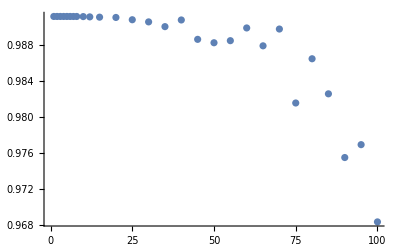

```mathematica
(* Can you make enough data to plot? *)
p=.0;
pSEr=.03;
UpdateErrorFunctions;
thisdata = GetPlotData[M,{"Logical Asymmetric Group","QEC at the End","Post Selection Discarded","Extract Expectation Values Directly"},100];
ListPlot[thisdata[[;;,1;;2]]]
```

#### Manage Multiple RB Sequences

```mathematica
GetPlotData[M_?ListQ,ModificationLabels_?ListQ,ncircuit_:defaultncircuit,ThisDecoding_:ListMWDecoding] :=
Module[{seqdata = {},evals ,outputs,mean,CI},

seqdata= Table[

evals = {};
If[MemberQ[ModificationLabels,"Extract Expectation Values Directly"],
evals=ParallelTable[RBSequence[m,ModificationLabels,ThisDecoding],{n,ncircuit}];,

Do[
outputs = ParallelTable[RBSequence[m,ModificationLabels,ThisDecoding],{n2,ncircuit2}];,
AppendTo[evals,StatswithPostSelection[evals,ModificationLabels][[1]]];
,{n,ncircuit}]

];

{mean,CI}=  StatswithPostSelection[evals,ModificationLabels];

{m,mean,CI,evals}

,{m,M}];

seqdata
];
```

```mathematica
(* Collect mean and confidence intervals taking into account the "PS" formatting for post-selection *)
StatswithPostSelection[output_?ListQ,ModificationLabels_?ListQ]:=Module[{nums},
nums=output;
If[ContainsAny[ModificationLabels,{"Post Selection Rejected"}],nums=output/."PS"->0];
If[ContainsAny[ModificationLabels,{"Post Selection Discarded"}],nums=DeleteCases[output,"PS"]];
If[nums==={},{"PS","N/A"},{Mean[nums],Quiet@Check[MeanCI[nums],"N/A"]} ]
];
```

```mathematica
(* Some additional parameters the user can adjust *)
ncircuit2= 100;
defaultncircuit=100;
M={1,2,3,4,5,6,7,8,10,12,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100};
QECatFixedTimeGatenum=50;
```

```mathematica
DataBase=<||>; (* Contains estimations of the survival probability *)
DataInfo=<||>; (* Info about how the data is taken *)
FitModels=  <||>;
Runlabels={};
model=A*Exp[r m]+ B;
```

```mathematica
Benchmark[Runlabel_,ModificationLabels_:{"LogicalAsymmetric"},ncircuit_:defaultncircuit,ThisDecoding_:ListMWDecoding]:= Module[{timebeforetimebefore,bysequencelength,timebefore,avgtime={},plotdata},

Runlabels=Union[Runlabels,{Runlabel}];
DataBase[Runlabel]=<||>;
DataInfo[ Runlabel]=<||>;

timebeforetimebefore = SessionTime[];

Table[

timebefore=SessionTime[];

{p,pSEr}={pErvals[[thisp]],pSErvals[[thispSEr]]};
UpdateErrorFunctions;

DataBase[ Runlabel][{p,pSEr}]=GetPlotData[M,ModificationLabels,ncircuit,ThisDecoding];

(* estimate time to completion *)
AppendTo[avgtime,SessionTime[]-timebefore];
Print[Runlabel," ",{p,pSEr}," | Tme to Benchmark Completion: ",DateObject[Mean@avgtime((Length@pErvals-thisp+1)*Length@pSErvals-thispSEr),"Second"], " Total Runtime: ",DateObject[SessionTime[]-timebeforetimebefore,"Second"]];
,{thisp,Range@Length@pErvals},{thispSEr,Range@Length@pSErvals}];

DataInfo[Runlabel]=GetCurrentDataInfo[Runlabel,ModificationLabels,ncircuit,ThisDecoding];

FitModels[Runlabel]=<||>;
Do[
plotdata=Flatten[(Table[{#[[1]],#[[2,i]]},{i,Length@#[[2]]}])&/@DataBase[Runlabel][errlabel][[;;,{1,4}]],1];
If[ContainsAny[ModificationLabels,{"Post Selection Rejected"}],plotdata=Flatten[(Table[{#[[1]],#[[2,i]]},{i,Length@#[[2]]}])&/@DataBase[Runlabel][errlabel][[;;,{1,4}]],1]/."PS"->0];
If[ContainsAny[ModificationLabels,{"Post Selection Discarded"}],plotdata=Flatten[(Table[{#[[1]],#[[2,i]]},{i,Length[#[[2]]]}])&/@DeleteCases[DeleteCases[DataBase[Runlabel][errlabel][[;;,{1,4}]],"PS",All],{i_,{}}],1];];

FitModels[Runlabel][errlabel]=NonlinearModelFit[plotdata,{model,-2<A<2,0<B<1,-2<r<0},{{A,.3},{B,.7},{r,-.1}},m];

,{errlabel,Keys@DataBase[Runlabel]}];

TempSave[];

]
```

## Benchmark

Runs character Benchmarking by default. Unless a QEC modifier is specified, it is assumed that the interleaved R is QEC. To do post-selection, one mush pick a QEC modifier below.
Any procedure that uses a tag from the first line should produce accurate results.

```mathematica
InterleavingGroupNames=Sequence@@Keys@SamplerAssoc;
Grid[{{"Available Iterleaving Groups: ",InterleavingGroupNames},{},
{"Sequence Modifiers: " ,"QEC Always","QEC at the End","QEC at Fixed Time","Measure Always Recover at the End"},{},
{"QEC Modifiers: ","Post Selection Rejected", "Post Selection Discarded"},{},
{"Data Gathering Techniques: ","Extract Expectation Values Directly"}}]
```

Available Iterleaving Groups:  | Logical Asymmetric Group | Logical Pauli Group | Stabilizer Group | Pure Error Group
 |  |  |  | 
Sequence Modifiers:  | QEC Always | QEC at the End | QEC at Fixed Time | Measure Always Recover at the End
 |  |  |  | 
QEC Modifiers:  | Post Selection Rejected | Post Selection Discarded |  | 
 |  |  |  | 
Data Gathering Techniques:  | Extract Expectation Values Directly |  |  |

### Plot Sequences for Appendix B

Discarded Post-selection threshold was too high for these noise rates. The graphs for discarded post-selection displayed int the thesis

```mathematica
pErvals={.0};
pSErvals={.03};
ncircuit= 10;
```

```mathematica
UpdateErrorFunctions=PhysicalOverrotation;
ThesisBenchmarks[];
```

```mathematica
UpdateErrorFunctions=DestabilizerOverrotation;
ThesisBenchmarks[];
```

```mathematica
Beep[];
```

```mathematica
ExponentialDecayRunlabels = {"Character Benchmarking","QEC Always","QEC End","Rejected Always","Rejected End"};
DoDiscarded=False;
ThesisBenchmarks := (

Benchmark["Character Benchmarking",{"Logical Asymmetric Group","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;

Benchmark["QEC Always",{"Logical Asymmetric Group","QEC Always","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["QEC End",{"Logical Asymmetric Group","QEC at the End","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["QEC Fixed Time",{"Logical Asymmetric Group","QEC at Fixed Time","Extract Expectation Values Directly"},ncircuit,ListMWDecoding];
TempSave[]; 

Benchmark["Rejected Always",{"Logical Asymmetric Group","QEC Always","Post Selection Rejected","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["Rejected End",{"Logical Asymmetric Group","QEC at the End","Post Selection Rejected","Extract Expectation Values Directly"},ncircuit,ListMWDecoding];
Benchmark["Rejected Fixed Time",{"Logical Asymmetric Group","QEC at Fixed Time","Post Selection Rejected","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
TempSave[];

If[DoDiscarded== True,
Benchmark["Discarded Always",{"Logical Asymmetric Group","QEC Always","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["Discarded End",{"Logical Asymmetric Group","QEC at the End","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["Discarded Fixed Time",{"Logical Asymmetric Group","QEC at Fixed Time","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
TempSave[]; 
];

DumpSave[NotebookDirectory[]<>"Thesis_Data_"<>ErrorName<>"("<>DateString[{"MonthShort","-","DayShort","-","YearShort"}]<>")"<>".mx",{DataBase,DataInfo,FitModels}];

ThisExponentialDecayRunlabels=Intersection[Keys@DataBase,ExponentialDecayRunlabels];
ptemp=p;
pSErtemp=pSEr;
Table[Export[NotebookDirectory[]<>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>If[ErrorName≠ "Depolarizing"," Overrotation",""],FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabeltemp][{ptemp,pSErtemp}][m],{m,-100,Max@DataInfo[Runlabeltemp]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}, {"R^2",FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]
],{Runlabeltemp,ThisExponentialDecayRunlabels }];

NonExponentialDecayRunlabels=DeleteCases[Keys@DataBase,Alternatives@@ExponentialDecayRunlabels];
If[DoDiscarded== False,NonExponentialDecayRunlabels=DeleteCases[NonExponentialDecayRunlabels,Alternatives@@{"Discarded Always","Discarded End","Discarded Fixed Time"}]];
Table[Export[NotebookDirectory[]<>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>If[ErrorName≠ "Depolarizing"," Overrotation",""],FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]}
}]
],{Runlabeltemp,NonExponentialDecayRunlabels}];


)
```

```mathematica
Table[Export[NotebookDirectory[]<>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>If[ErrorName≠ "Depolarizing"," Overrotation",""],FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabeltemp][{ptemp,pSErtemp}][m],{m,-100,Max@DataInfo[Runlabeltemp]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}, {"R^2",FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]
],{Runlabeltemp,ThisExponentialDecayRunlabels }];
```

### Test to see if Recovery can be Delayed

```mathematica
ncircuit=50;
pErvals={.0};
pSErvals={.06,.1};
UpdateErrorFunctions=PhysicalOverrotation;
```

```mathematica
Benchmark["QEC Always",{"Logical Asymmetric Group","QEC Always","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Measure Always Recovery at the End",{"Logical Asymmetric Group","Measure Always Recover at the End","Extract Expectation Values Directly"},ncircuit,ListMWDecoding]
PassiveVsActiveSave;
```

```mathematica
PassiveVsActiveRunlabels ={"QEC Always","Measure Always Recovery at the End"};
PassiveVsActiveSave:=(
DumpSave["PassiveVsActive_"<>ErrorName<>"("<>DateString[{"MonthShort","-","DayShort","-","YearShort"}]<>")"<>".mx",{DataBase,DataInfo,FitModels}];


ptemp=p;
Table[Export[NotebookDirectory[]<>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName <>"_"<>ToString@Round@(pSErtemp*100) <>"_percent"<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>If[ErrorName≠ "Depolarizing"," Overrotation",""],FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabeltemp][{ptemp,pSErtemp}][m],{m,-100,Max@DataInfo[Runlabeltemp]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}, {"R^2",FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]
],{Runlabeltemp,PassiveVsActiveRunlabels },{pSErtemp,pSErvals}];
)
```

### Discarded Post-Selection with Non-standard Decay

```mathematica
ncircuit=10;
pErvals={.0};
pSErvals={.06};
```

```mathematica
UpdateErrorFunctions=PhysicalOverrotation;
Benchmark["Discarded Always",{"Logical Asymmetric Group","QEC Always","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
Benchmark["Discarded End",{"Logical Asymmetric Group","QEC at the End","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] ;
DiscardSave[];
TempSave[];
```

```mathematica
Beep[];
```

```mathematica
DiscardSave:=(
DumpSave[NotebookDirectory[]<>"Dicarded_"<>ErrorName<>"("<>DateString[{"MonthShort","-","DayShort","-","YearShort"}]<>")"<>".mx",{DataBase,DataInfo,FitModels}];

DiscardedRunlabels={"Discarded Always","Discarded End"};
ptemp=p;
pSErtemp=pSEr;
Table[Export[NotebookDirectory[]<>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>If[ErrorName≠ "Depolarizing"," Overrotation",""],FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]}
}]
],{Runlabeltemp,DiscardedRunlabels}];
)
```

### Plot a Variety of Common Sequences with Common Names

```mathematica
ncircuit= 200;
Benchmark["Character Benchmarking",{"Logical Asymmetric Group","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Logical RB",{"Logical Asymmetric Group","QEC Always","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["IBMQ Real RB With Post Selection",{"Logical Asymmetric Group","QEC at the End","Post Selection Rejected","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Passive Logical RB",{"Logical Asymmetric Group","Measure Always Recover at the End","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["QEC at the End RB",{"Logical Asymmetric Group","QEC at the End","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Discarded Post Selection at the End RB",{"Logical Asymmetric Group","QEC at the End","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["QEC at Fixed Time RB",{"Logical Asymmetric Group","QEC at Fixed Time","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Rejected Post Selection at Fixed Time RB",{"Logical Asymmetric Group","QEC at Fixed Time","Post Selection Rejected","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Discarded Post Selection at Fixed Time RB",{"Logical Asymmetric Group","QEC at Fixed Time","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding] 
Benchmark["Discarded Post Selection Always LFE",{"Logical Asymmetric Group","QEC Always","Post Selection Discarded","Extract Expectation Values Directly"},ncircuit,ListMWDecoding]
```

## Save, Display, and Retrieve Data

### Survival Probability Plot

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
SetOptions[Grid,BaseStyle->{FontFamily->"Times",FontSize->14}];
DataGathered=False;
```

Error Bars may be a little bit wonky for low sample sizes.

```mathematica
DataGathered=True;
Manipulate[
Manipulate[If[DataGathered,
ptemmp=p;
pSErtemp = pSEr;
Runlabeltemp=Runlabel;
Grid[{
{Show[ListPlot[DataBase[Runlabel][{p,pSEr}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[Runlabel<>"\n in the [["<>ToString@Code[[1]]<>"," <>ToString@Code[[2]]<> "," <>ToString@Code[[3]]<>"]] Code",FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabel]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabel][{p,pSEr}][m],{m,-100,Max@DataInfo[Runlabel]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabel][{p, pSEr}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabel][{p, pSEr}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabel][{p,pSEr}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabel][{p,pSEr}]["BestFitParameters"]}, {"R^2",FitModels[Runlabel][{p,pSEr}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabel][{p,pSEr}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]]

,{p,DataInfo[Runlabel]["Controlable Error Range"][[1]]},{pSEr,DataInfo[Runlabel]["Controlable Error Range"][[2]]}],{Runlabel,Keys@DataBase}]
```

### Export Data

```mathematica
(* Export current plot *)
Export[NotebookFileName[]<>"Discarded_Fixed_Time_Physical.png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  Destabilizer Overrotation",FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabeltemp][{ptemp,pSErtemp}][m],{m,-100,Max@DataInfo[Runlabeltemp]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabeltemp][{p,pSEr}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabeltemp][{p,pSEr}]["BestFitParameters"]}, {"R^2",FitModels[Runlabeltemp][{p,pSEr}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabeltemp][{p,pSEr}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]
];
```

```mathematica
(*  Export All Plots with same error model  for comparison *)
ptemp=0.;
pSErtemp=.03;
Table[Export[NotebookFileName[] <>StringReplace[Runlabeltemp," "-> "_"]<>"_"<>ErrorName<>".png",
Grid[{
{Show[ListPlot[DataBase[Runlabeltemp][{ptemp,pSErtemp}][[;;,1;;2]],Frame->{{True,False},{True,False}},ImageSize->{800,500},FrameLabel->{{"Survival  Probability ",None},{"Sequence Length",None}},PlotLabel->Style[ToString@Round@(pSErtemp*100) "%  "<>ErrorName<>" Overrotation",FontFamily->"Times",FontSize->20],PlotRange->{{0,Max@DataInfo[Runlabeltemp]["M"]+1},{-.03,1.03}},ImageSize->Large],
Plot[FitModels[Runlabeltemp][{ptemp,pSErtemp}][m],{m,-100,Max@DataInfo[Runlabeltemp]["M"]},PlotStyle->{Red,Thick}],
ListPlot[{Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[;;;;2]],
Flatten[(Table[{#[[1]],#[[2,i]]},{i,2}])&/@(DataBase[Runlabeltemp][{ptemp, pSErtemp}][[;;,{1,3}]]/."N/A"->{-1,-1}),1][[2;;;;2]]},PlotMarkers-> {Graphics[{Blue,Line[{{.05,0},{0,0}}]}],Graphics[{Blue,Line[{{.05,0},{0,0}}]}]},Filling-> {2->{1}},FillingStyle->Blue]]},

{Grid[{{"Fidelity",E^(r/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]),"         "  ,"A",A/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}, {"R^2",FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["AdjustedRSquared"],"         ","B",B/.FitModels[Runlabeltemp][{ptemp ,pSErtemp}]["BestFitParameters"]}},Alignment->Center,ItemStyle->{FontFamily->"Times",FontSize->20}]}
}]
],{Runlabeltemp,Keys@DataBase}];
```

### Save and Manipulate Data

I save data in .mx files in 3 association {DataBase,DataInfo,FitModels} as you can see below. 

DataBase shows raw physical data for each procedure
DataInfo gives various specs on the RB run including error model description, gate set used, sequence lengths tested, etc...
FitModels is an association of NonLinearModelFit Objects for each of the benchmarks in DataBase https://reference.wolfram.com/language/ref/NonlinearModelFit.html

```mathematica
TempSave := DumpSave[NotebookDirectory[]<>"temp"<>"("<>DateString[{"MonthShort","-","DayShort","-","YearShort"}]<>")"<>".mx",{DataBase,DataInfo,FitModels}];
```

```mathematica
CoreName="Ignored_Entangled_Accurate(1-7-21)";
DumpSave[NotebookDirectory[]<>CoreName<>"("<>DateString[{"MonthShort","-","DayShort","-","YearShort"}]<>")"<>".mx",{DataBase,DataInfo,FitModels}];
```

```mathematica
(* Save data before new data is loaded and erases these variables *)
TempDataBase=DataBase;
TempDataInfo=DataInfo;
TempFitModels = FitModels;
```

```mathematica
DataBase[Runlabel][Errlabel][[i, 4]]=TempDataBase[Runlabel][Errlabel][[i, 4]]
```

```mathematica
TempDataBase["QEC Always"][{0.,.08} ][[20, 4]]== DataBase["QEC Always"][{0.,.08} ][[20, 4]]
```

True

```mathematica
(* Use this here to retrieve data! *)
```

```mathematica
Get[(* Place .mx file name here! *)]
DataGathered=True;
```

```mathematica
GetCurrentDataInfo[Runlabel_?StringQ,ModificationLabels_?ListQ,ncircuit_?IntegerQ,Decoding_?ListQ]:=Module[{tempassn=<||>,ThisDecoding},

ThisDecoding=Decoding;

tempassn["Controlable Error Range"]={pErvals,pSErvals};
tempassn["Error Model"]=UpdateErrorFunctions;
tempassn["Error Model Description"]=ErrorModelDescription;
tempassn["Modification Labels"]=ModificationLabels;
tempassn["Decoding"]=If[ContainsAny[ModificationLabels,{"Post Selection Rejected", "Post Selection Discarded"}],Do[ThisDecoding[[i]]=ListZero,{i,2,Length@ThisDecoding}],ThisDecoding];
tempassn["ncircuit"]=ncircuit;
tempassn["ncircuit2"]=If[MemberQ[ModificationLabels,"Extract Expectation Values Directly"],"NA",ncircuit2];
tempassn["M"]=M;

tempassn

]
```

## Debugging and Memory Usage

### Memory Usage

Because of memoization we can find that sometimes we are saving more than we need to save. If memory overflows, Here’s where we detect & diagnose it.

```mathematica
myByteCount[symbolName_String]:=Replace[ToHeldExpression[symbolName],Hold[x__]:>If[MemberQ[Attributes[x],Protected|ReadProtected],Sequence@@{},{ByteCount[Through[{OwnValues,DownValues,UpValues,SubValues,DefaultValues,FormatValues,NValues}[Unevaluated@x,Sort->False]]],symbolName}]];

CheckVariablesMemoryUsage[numvars_:100]:=With[{listing=myByteCount/@Names[]},Labeled[Grid[Reverse@Take[Sort[listing],-numvars],Frame->True,Alignment->Left],Column[{Style["ByteCount for symbols without attributes Protected and ReadProtected in all contexts",16,FontFamily->"Times"],Style[Row@{"Total: ",Total[listing[[All,1]]]," bytes for ",Length[listing]," symbols"},Bold]},Center,1.5],Top]]
```

```mathematica
CheckVariablesMemoryUsage[100]
```

```mathematica
{{3757552, "AllListPaulis"}, {3447576, "PacletManager`Services`Private`$pacletSiteData"}, {2303712, "ToListString"}, {1793008, "FullAllPaulisCodeOrder"}, {1760752, "AllPaulisCodeOrder"}, {1740880, "LRep"}, {1740600, "StateLRep"}, {1740024, "AllPaulis"}, {1639048, "DSGroup"}, {1263624, "Parallel`Parallel`Private`$distributedDefs"}, {1247384, "System`DateCalendarsDump`EarthVSOPD"}, {851360, "PacletManager`Manager`Private`$basePathMap"}, {851328, "PacletManager`Manager`Private`$pathMap"}, {591480, "SingleQubitMult"}, {454240, "PacletManager`Collection`Private`$layoutPacletCollection"}, {440128, "Interpreter`PackageScope`validateOption"}, {419000, "MessageMenu`MessageStackList"}, {378352, "AllPauliStrings"}, {287856, "Interpreter`Transform`PackagePrivate`transformType"}, {219872, "System`DateCalendarsDump`col2"}, {219872, "System`DateCalendarsDump`col1"}, {219808, "System`DateCalendarsDump`col3"}, {204704, "Statistics`SurvivalModelFitDump`iSMProperty"}, {200816, "DynamicDump`ControlToBoxes"}, {198440, "Manipulate`Dump`parameterToControls"}, {189568, "System`DateCalendarsDump`LunarPositionX"}, {186760, "System`TimeZonesDump`timeZoneNameShort"}, {183632, "FileFormatDump`$FILEFORMATMATRIX"}, {173072, "DataBase"}, {163576, "Interpreter`InterpreterObject"}, {161032, "Templating`PackageScope`toHTMLNode"}, {147224, "SyndOutcomeProj"}, {143248, "PersistenceLocations`Dump`$icons"}, {127696, "AGroup"}, {119616, "RandomProcesses`TemporalDataDump`iProperty"}, {106120, "NormPhase"}, {103344, "Image`InteractiveImageDump`oDynamicImage"}, {100080, "CloudObject`Private`validateDocGenArg"}, {95104, "System`ProtoPlotDump`iListPlot"}, {94488, "SymbolicTensors`SymbolicTensorsDump`TensorExpandRule"}, {90424, "SymbolicTensors`SymbolicTensorsDump`$TensorExpandRules"}, {85512, "Image`ColorOperationsDump`oImageEffect"}, {83280, "Legending`LegendDump`legendLayout"}, {77896, "System`ProtoPlotDump`iPlot"}, {75840, "System`Dump`ParameterValidation`AssumedInSpec"}, {72336, "System`DateStringDump`convertDateStringForms"}, {70632, "Legending`LegendDump`iColorGradientLegend"}, {69128, "RBSequence"}, {68336, "ListGate"}, {66584, "Interpreter`PackageScope`$IPv6Address"}, {65232, "NAGroup"}, {64032, "Interpreter`PackageScope`$CountryCodes"}, {63240, "System`DateCalendarsDump`MonthBlueMoons"}, {62808, "PacletManager`Collection`Private`$userPacletCollection"}, {62216, "Legending`LegendDump`plotLegendParser"}, {62176, "DGroup"}, {62176, "ListDDecoding"}, {61760, "System`Dump`ParameterValidation`ExplicitlyInSpec"}, {61584, "PacletManager`Package`$managerData"}, {61472, "Benchmark"}, {60576, "Legending`LegendDump`iFixedSwatchLegend"}, {60248, "GetPlotData"}, {59784, "ListLogicalMWDecoding"}, {59544, "SGroup"}, {58848, "CloudObject`Private`$httpRules"}, {58152, "Legending`LegendDump`assembleLegendContainer"}, {57544, "ThisDecoding$4356"}, {57544, "ListMWDecoding"}, {57544, "ListDecoding"}, {56984, "ListIdDecoding"}, {56776, "DynamicDump`ControlToExpression"}, {55728, "FittedModels`FittedModelDump`iLinearProps"}, {55664, "CloudObject`Private`bannerImgr"}, {55536, "System`Dump`defaultPacletIcon"}, {55128, "Image`ImageDump`expandSpan"}, {54776, "System`ProtoPlotDump`iListContourPlot"}, {53792, "GeneralUtilities`Formatting`PackagePrivate`fullbox"}, {52696, "Image`CompositionOperationsDump`oWordCloud"}, {52680, "System`Dump`AddCache"}, {52024, "Manipulate`Dump`toPeriodicFunction"}, {51208, "FullAllPauliGensCodeOrder"}, {50496, "System`GeoGraphicsDump`EstimateRangesAndProjection"}, {50256, "Legending`LegendDump`iLegendConstructer"}, {49112, "System`ProtoPlotDump`iListDensityPlot"}, {48936, "Semantic`PLIDump`processSubPattern"}, {47992, "Image`ColorOperationsDump`oGradientImage"}, {47960, "System`Dump`anpts"}, {47840, "System`ProtoPlotDump`iContourPlot"}, {47776, "Explore`ExploreDump`MakeExploreBoxes"}, {47224, "System`Dump`ParameterValidation`SpecAssumptions"}, {47120, "Manipulate`Dump`updateOneVar"}, {46416, "Legending`LegendDump`legendNames"}, {46152, "System`Dump`RemoveCache"}, {44664, "RandomProcesses`TemporalDataDump`timeFilter"}, {44448, "System`GeoGraphicsDump`GeoGraphicsOptionsParse"}, {44328, "AllPauliGensCodeOrder"}, {44232, "Image`CompositionOperationsDump`iImageCollage"}, {43272, "Legending`LegendDump`iColorBandLegend"}, {43008, "System`InfoDump`formatRow"}, {42864, "Interpreter`InternalColor`PackagePrivate`$W3CNamedColors"}}{{"ByteCount for symbols without attributes Protected and ReadProtected in all contexts"}, {"Total: "73007737" bytes for "40288" symbols"}}
```